# Nanobot Theory : Data Analysis and Plotting

#### Yibin Jiang, Abhishek Sharma Cronin Lab University of Glasgow

```mathematica
deviationslLLP[ave_,dev_,opts:OptionsPattern[]]:=Module[{
fill=Join@@(Thread[Range[Length@ave]->List/@(Length[ave] #+Range[Length@ave])]&/@{1,2}),
apd=Style[#,Opacity[0]]&/@(ave+dev),
amd=Style[#,Opacity[0]]&/@(ave-dev),p1,p2},
p1=ListLinePlot[Join@@{ave,apd,amd},Filling->fill,opts]
]
```

```mathematica
data = Reverse[Import[NotebookDirectory[]<>"/ratioes.csv"],2];
```

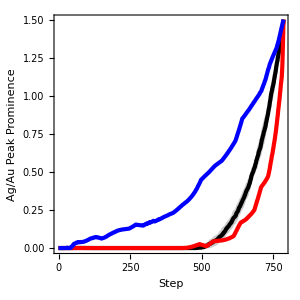

```mathematica
f1 = deviationslLLP[
{Mean[data⟦1;;10⟧]},
{StandardDeviation[data⟦1;;10⟧]},
PlotStyle->{{Black,Thickness[0.010]}},
DataRange->{0,Length@data⟦12⟧-1},
AspectRatio->1,
PlotRange->Full,
PlotLegends->Placed[{"Random"},{0.2,0.8}],
LabelStyle->{Directive[Black,FontColor->Black,FontSize->14]},
FrameLabel->{"Step","Ag/Au Peak Prominence"},
Frame->True,
FrameStyle->{{{Thick,Thick},Thick},{Thick,Thick}},
FrameTicksStyle->{{Thick,Thick},{{Thick},Thick}},
ImageSize->300];
f2 = ListLinePlot[
data⟦11⟧,
PlotStyle->{{Blue,Thickness[0.010]}},
AspectRatio->1,
DataRange->{0,Length@data⟦12⟧-1},
PlotRange->Full,
PlotLegends->Placed[{"Tip"},{0.2,0.8}],
LabelStyle->{Directive[Black,FontColor->Black,FontSize->14]},
FrameLabel->{"Step","Ag/Au Peak Prominence"},
Frame->True,
FrameStyle->{{{Thick,Thick},Thick},{Thick,Thick}},
FrameTicksStyle->{{Thick,Thick},{{Thick},Thick}},
ImageSize->300];
f3 = ListLinePlot[
data⟦12⟧,
PlotStyle->{{Red,Thickness[0.010]}},
AspectRatio->1,
PlotRange->Full,
PlotLegends->Placed[{"Centre"},{0.2,0.8}],
DataRange->{0,Length@data⟦12⟧-1},
LabelStyle->{Directive[Black,FontColor->Black,FontSize->14]},
FrameLabel->{"Step","Ag/Au Peak Prominence"},
Frame->True,
FrameStyle->{{{Thick,Thick},Thick},{Thick,Thick}},
FrameTicksStyle->{{Thick,Thick},{{Thick},Thick}},
ImageSize->300];
f = Show[{f1,f3,f2},PlotRange->Full]
```

```mathematica
Export[NotebookDirectory[]<>"/prominence.png",f,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Nanobot_Theory-Yibin-Abhishek\Code\Au@Ag octahedra\/prominence.png